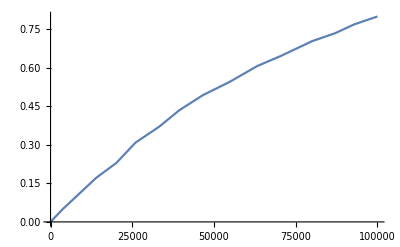

```mathematica
ListLinePlot[{Rescale[h2]*1*^5,Rescale[b2]*.8}//Transpose]
```

```mathematica
ImportString["0 0
0.73 400
0.92 600
1.05 800
1.15 1000
1.28 1400
1.42 2000
1.52 3000
1.58 4000
1.6 6000","Data"]
```

{{0,0},{0.73,400},{0.92,600},{1.05,800},{1.15,1000},{1.28,1400},{1.42,2000},{1.52,3000},{1.58,4000},{1.6,6000}}

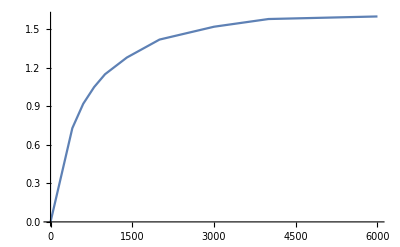

```mathematica
ListPlot[Reverse/@{{0,0},{0.73,400},{0.92,600},{1.05,800},{1.15,1000},{1.28,1400},{1.42,2000},{1.52,3000},{1.58,4000},{1.6,6000}},Joined->True]
```

```mathematica
f=Interpolation[Reverse/@{{0,0},{0.73,400},{0.92,600},{1.05,800},{1.15,1000},{1.28,1400},{1.42,2000},{1.52,3000},{1.58,4000},{1.6,6000}}]
```

InterpolatingFunction[…]

```mathematica
data=Table[{f[x],f[x]/x},{x,1,6000,1}];
```

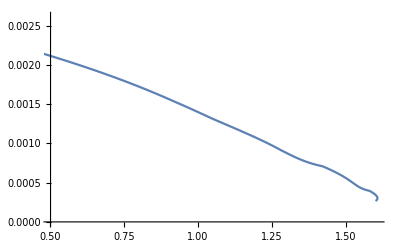

```mathematica
ListLinePlot[data]
```

```mathematica
data[[1]]
```

{0.,Indeterminate}

```mathematica
{h,b}={{47.21367010088071,44.70645760116514},{50.53463852973591,47.10087096176409},{53.06559684776213,49.23194761875345},{55.27469919470985,53.82896118547029},{56.67591054354646,58.85186497654354},{57.75526592130458,62.982349938717334},{58.818365946988045,68.36449701064072},{60.382130816571355,76.47916876631632},{60.382130816571355,81.14120374133182},{61.08923863181952,89.70127214385337},{61.7963464470677,99.35370020579273},{61.7963464470677,107.59841477806566},{61.7963464470677,112.81963386444988},{62.505079797523344,120.52629628305118},{62.623743867668416,128.08015839215062},{63.46414556992891,135.28615596685205},{63.57143089362172,142.518162104873},{64.70768000364117,148.38959527424404},{66.07312957791353,156.97892331049997},{67.54098787025629,167.28806759625604},{69.44936620382259,178.18403009190774},{72.11036733844617,188.28022926548564},{74.63970012126492,193.72739774570775},{77.25681180528687,198.59587569207162},{81.3661648097636,203.1311189209047},{86.99864430363698,206.85359454600425},{93.68772168236393,212.9265940811012},{99.25680530314605,215.18446248427293},{106.1539511884288,218.69724406760923},{113.3778296504124,220.805563231694},{121.93139591210405,222.6131583823974},{135.504614894454,224.07126346349534},{143.65017181907146,225.47247481233194},{152.74991791047202,226.16332727550545},{168.61026492972812,227.75635177882316},{186.2668283532353,230.39134435012727},{208.09451511910297,231.6917725161009},{231.79319290876518,231.4446911645659},{246.70585290206802,233.04421780871346},{260.52615323595285,233.04421780871346},{272.95662096745343,234.19509673560015},{292.5313159357718,235.39961832433326},{310.0155726272875,235.20130302902226},{324.5250998891384,236.91461713769257},{331.60268018245,237.14381760194541},{342.7099622550724,237.98747037462084},{358.35248755652793,237.46729910823137},{369.7263574031749,238.92052758370693},{380.0176208016489,239.14160037192244},{392.44646299794204,237.90294254383255},{403.5098556199628,239.12697055505524},{413.75560403262773,239.56749059627876},{425.1473547665569,239.56749059627876},{435.05661739127606,240.36725391835256},{448.2397079238339,240.31036018609126},{461.8145524413913,240.83540805810313},{472.5593401627486,241.19627687416082},{482.4751049282975,241.92939325272846}}//Transpose
```

{{47.2137,50.5346,53.0656,55.2747,56.6759,57.7553,58.8184,60.3821,60.3821,61.0892,61.7963,61.7963,61.7963,62.5051,62.6237,63.4641,63.5714,64.7077,66.0731,67.541,69.4494,72.1104,74.6397,77.2568,81.3662,86.9986,93.6877,99.2568,106.154,113.378,121.931,135.505,143.65,152.75,168.61,186.267,208.095,231.793,246.706,260.526,272.957,292.531,310.016,324.525,331.603,342.71,358.352,369.726,380.018,392.446,403.51,413.756,425.147,435.057,448.24,461.815,472.559,482.475},{44.7065,47.1009,49.2319,53.829,58.8519,62.9823,68.3645,76.4792,81.1412,89.7013,99.3537,107.598,112.82,120.526,128.08,135.286,142.518,148.39,156.979,167.288,178.184,188.28,193.727,198.596,203.131,206.854,212.927,215.184,218.697,220.806,222.613,224.071,225.472,226.163,227.756,230.391,231.692,231.445,233.044,233.044,234.195,235.4,235.201,236.915,237.144,237.987,237.467,238.921,239.142,237.903,239.127,239.567,239.567,240.367,240.31,240.835,241.196,241.929}}

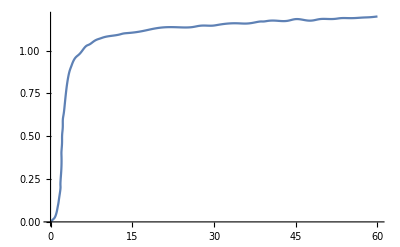

```mathematica
ListLinePlot[{h,b}//Transpose,InterpolationOrder->4]
```

```mathematica
{h,b}={Rescale[h]*60,Rescale[b]*1.2}
```

{{0.,0.457789,0.806677,1.1112,1.30435,1.45314,1.59969,1.81525,1.81525,1.91272,2.0102,2.0102,2.0102,2.10789,2.12425,2.2401,2.25489,2.41152,2.59974,2.80208,3.06515,3.43196,3.78063,4.14139,4.70786,5.48429,6.40636,7.17405,8.12481,9.12061,10.2997,12.1707,13.2936,14.548,16.7343,19.1682,22.1771,25.444,27.4996,29.4047,31.1183,33.8166,36.2268,38.2269,39.2025,40.7336,42.8899,44.4578,45.8764,47.5897,49.1148,50.5271,52.0975,53.4634,55.2807,57.152,58.6331,60.},{0.,0.0145688,0.0275353,0.0555057,0.0860675,0.111199,0.143947,0.193321,0.221687,0.27377,0.3325,0.382665,0.414434,0.461325,0.507286,0.551131,0.595134,0.630858,0.68312,0.745846,0.812142,0.873572,0.906716,0.936338,0.963932,0.986582,1.02353,1.03727,1.05864,1.07147,1.08247,1.09134,1.09987,1.10407,1.11376,1.1298,1.13771,1.13621,1.14594,1.14594,1.15294,1.16027,1.15906,1.16949,1.17088,1.17602,1.17285,1.18169,1.18304,1.1755,1.18295,1.18563,1.18563,1.1905,1.19015,1.19334,1.19554,1.2}}

```mathematica
FindFit[Transpose[{b,b/h}]⟦1;;-2⟧,a1 ⅇ^(-(x-b1)^2/c1^2)+a2/((1+ⅇ^(-(x-b2)^2/c2^2))^2),{a1,a2,b1,b2,c1,c2},x]
```

{a1→0.0278545,a2→-0.0327142,b1→1.21907,b2→-0.446836,c1→1.29066,c2→1.66763}

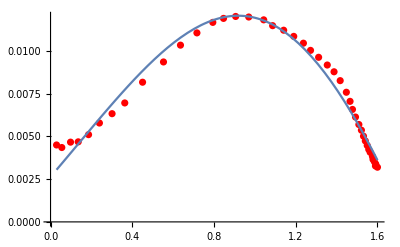

```mathematica
Show[ListPlot[Transpose[{b,b/h}]⟦1;;-2⟧,PlotStyle->Red],Plot[a1 ⅇ^(-(x-b1)^2/c1^2)+a2/((1+ⅇ^(-(x-b2)^2/c2^2))^2)/.{a1->0.0278545239021253,a2->-0.032714158726535554,b1->1.2190700421157294,b2->-0.44683612112455195,c1->1.2906617169549084,c2->1.667632260179665},{x,0.029456972393568304,1.6}]]
```

```mathematica
?InterpolatingPolynomial
```

```mathematica
order=6
FindFit[Transpose[{b,b/h}]⟦1;;-2⟧,Sum[Subscript[a, i]*x^i,{i,0,order}],Table[Subscript[a, i],{i,0,order}],x]
```

6

{a_0→0.00448372,a_1→-0.00221578,a_2→0.0348159,a_3→-0.0188674,a_4→-0.026502,a_5→0.0278608,a_6→-0.00765004}

```mathematica
1/(∑_(i=0)^order Subscript[a, i] x^i/.%202)
```

1/(0.00448372-0.00221578 x+0.0348159 x^2-0.0188674 x^3-0.026502 x^4+0.0278608 x^5-0.00765004 x^6)

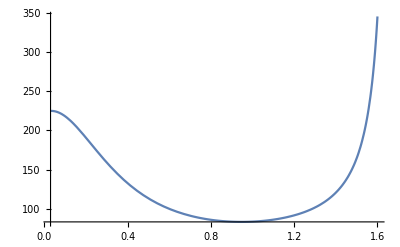

```mathematica
Show[Plot[1/(∑_(i=0)^order Subscript[a, i] x^i/.%202),{x,0.029456972393568304,1.6}]]
```

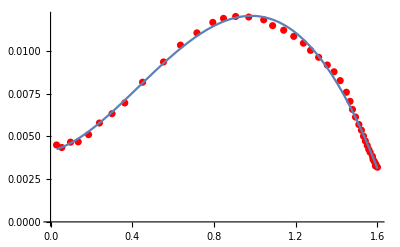

```mathematica
Show[ListPlot[Transpose[{b,b/h}]⟦1;;-2⟧,PlotStyle->Red],Plot[∑_(i=0)^4 Subscript[a, i] x^i/.{Subscript[a, 0]->0.004158806849119841,Subscript[a, 1]->0.0026704768338732887,Subscript[a, 2]->0.021755180431632673,Subscript[a, 3]->-0.01926561010391445,Subscript[a, 4]->0.002732150995166917},{x,0.029456972393568304,1.6}]]
```

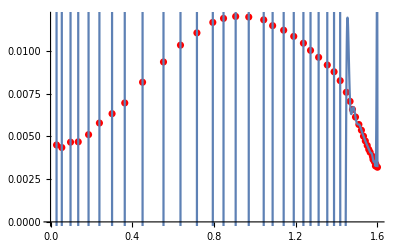

```mathematica
Show[ListPlot[Transpose[{b,b/h}]⟦1;;-2⟧,PlotStyle->Red],Plot[0.0032+(-0.0008290141762688902+(-0.012670760561694888+(-0.007225613263236899+(0.006847791221901041+(-0.01132934050272097+(-0.0022070890502469106+(-0.0024618804565816267+(0.05377742063601941+(0.2261326114531553+(0.21376775448579916+(0.3588154412166449+(1.715912696138917+(-6.03010422402147+(-6.729649774431529+(-11.0871025716942+(71.68504323236073+(126.47235682347623+(470.30553389752345+(-1350.4374474061112+(-1972.4576555167894+(-3851.464758178704+(-3684.800633894914+(-14301.131453457345+(59465.47445414367+(-12418.784941468739+(86785.83261535142+(1.0936810683157666*^7+(2.2340062342270233*^7+(-1.7600237298136786*^8+(-4.421731624177841*^8+(-5.971994625460053*^9+(3.340276481560286*^10+(-2.9951666219332745*^11+(2.783963306357375*^12+(-5.427485464466332*^13+(-1.146920114655108*^15+(5.642336628109026*^16+(-2.2687213789253297*^18+(-3.233554885716457*^19+(-2.2652871721290084*^21+(-2.6898799564144576*^23-8.339027807956512*^24 (-1.5783496814642533+x)) (-1.5316412175144096+x)) (-1.5901708969562138+x)) (-1.50903023561533+x)) (-1.4658408332490644+x)) (-1.5642026494084336+x)) (-1.492547274749722+x)) (-1.4175851956719585+x)) (-1.5753867934068153+x)) (-1.2375872181211445+x)) (-1.3120335726564871+x)) (-1.5406310041460207+x)) (-1.0869147537668116+x)) (-0.846597229244615+x)) (-1.4477399130346849+x)) (-1.5914551521893012+x)) (-0.9700374153099403+x)) (-0.7164526241278187+x)) (-1.354393770856507+x)) (-0.2391849529780563+x)) (-1.1409647082617047+x)) (-0.36325209829103033+x)) (-1.52145818586308+x)) (-0.09787642835473731+x)) (-0.6359591465264436+x)) (-1.585033876023865+x)) (-1.1902922439073718+x)) (-0.1860451006168468+x)) (-1.3875113762766709+x)) (-0.4504095459601576+x)) (-0.9060268985741731+x)) (-0.05512185256345408+x)) (-1.5573768834058042+x)) (-0.5527960359995954+x)) (-1.0432905248255635+x)) (-0.13550409545960146+x)) (-1.4777227222166043+x)) (-0.3011022348063504+x)) (-1.2724036808575185+x)) (-0.7941955708362827+x)) (-0.029456972393568304+x)) (-1.6+x),{x,0,1.6}]]
```

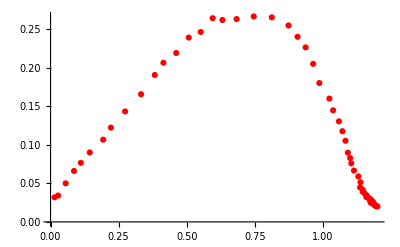

```mathematica
Show[ListPlot[Transpose[{b,b/h}]⟦2;;All⟧,PlotStyle->Red],Plot[1/(a1 ⅇ^(-(x-b1)^2/c1^2)+a2/((1+ⅇ^(-(x-b2)^2/c2^2))^2)/.{a1->0.5487730526102833,a2->-0.5524275787243602,b1->0.829184143062798,b2->-0.1693457629427381,c1->0.7439994904350314,c2->-0.9866129863856529}),{x,0.014568772253725248,1.2}]]
```

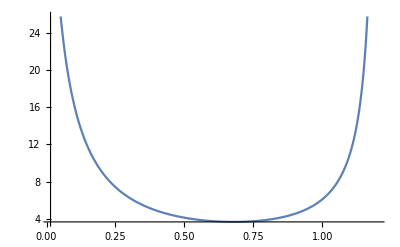

```mathematica
Plot[1/(a1 ⅇ^(-(x-b1)^2/c1^2)+a2/((1+ⅇ^(-(x-b2)^2/c2^2))^2)/.{a1->0.5487730526102833,a2->-0.5524275787243602,b1->0.829184143062798,b2->-0.1693457629427381,c1->0.7439994904350314,c2->-0.9866129863856529}),{x,0.014568772253725248,1.2}]
```

```mathematica
{h,b}={{1453.3076430534732,1040.8057911148594},{1418.2399230072463,1035.6762465121608},{1378.1534818528235,1036.3464647884393},{1331.5442864505246,1032.9953734070466},{1286.4866199712642,1029.507071984841},{1234.2729221326836,1027.9608203710645},{1168.6970772426287,1022.1241163272532},{1127.7926531525902,1018.5619325753792},{1076.9985515054973,1014.6461691029486},{1024.8112402132267,1009.8227084374481},{976.0752891783275,1005.1311805034984},{922.5369867149758,999.8169300766285},{876.8091019594369,993.3311169935866},{823.9251858445776,984.7291028964686},{778.1392506871564,976.9925675183243},{737.0553980822089,970.7917291354324},{695.4596464788439,961.3453455563886},{648.0852412335498,945.6084093369983},{614.8751340475595,929.9136915917043},{589.348789147093,912.6305037585375},{561.6006970473096,890.5238552598703},{538.4596959332833,869.8420802619526},{517.8043074816758,851.6723044727637},{496.46814613526567,826.990329054223},{477.0634799787606,801.2476144740132},{459.73807367149755,773.0403964684326},{444.01696937989334,750.2740843120108},{426.058285961186,712.0452560178246},{412.4692146114443,678.639888389139},{401.9990330355655,647.6251418561554},{394.47886733716473,620.2781252602867},{386.5154076607529,579.7061716537567},{378.4569564176245,537.6987899279529},{372.5147061885723,494.29819855697167},{362.8150117649508,440.86544227886077},{355.6589804056305,395.38031374937555},{344.2916562552057,362.94597102490445},{329.0666190342329,330.6330064134602},{317.0554631538397,302.9007462414628},{298.64820844785936,276.5247545498087},{279.15910534316174,256.88788678577396},{258.79924621022815,234.57542322588722},{243.79585597826085,221.18161231884073},{227.7581131309345,205.80881043853105}}//Transpose
```

{{1453.31,1418.24,1378.15,1331.54,1286.49,1234.27,1168.7,1127.79,1077.,1024.81,976.075,922.537,876.809,823.925,778.139,737.055,695.46,648.085,614.875,589.349,561.601,538.46,517.804,496.468,477.063,459.738,444.017,426.058,412.469,401.999,394.479,386.515,378.457,372.515,362.815,355.659,344.292,329.067,317.055,298.648,279.159,258.799,243.796,227.758},{1040.81,1035.68,1036.35,1033.,1029.51,1027.96,1022.12,1018.56,1014.65,1009.82,1005.13,999.817,993.331,984.729,976.993,970.792,961.345,945.608,929.914,912.631,890.524,869.842,851.672,826.99,801.248,773.04,750.274,712.045,678.64,647.625,620.278,579.706,537.699,494.298,440.865,395.38,362.946,330.633,302.901,276.525,256.888,234.575,221.182,205.809}}

```mathematica
{h,b}={Rescale[h],Rescale[b]}*{500,1.6}
```

{{500.,485.693,469.339,450.323,431.94,410.638,383.885,367.196,346.473,325.182,305.299,283.456,264.8,243.224,224.545,207.783,190.813,171.485,157.936,147.522,136.201,126.76,118.333,109.628,101.712,94.6432,88.2293,80.9026,75.3585,71.0869,68.0188,64.7698,61.4822,59.0578,55.1005,52.181,47.5434,41.3319,36.4316,28.9218,20.9706,12.6642,6.54308,0.},{1.6,1.59017,1.59146,1.58503,1.57835,1.57539,1.5642,1.55738,1.54987,1.54063,1.53164,1.52146,1.50903,1.49255,1.47772,1.46584,1.44774,1.41759,1.38751,1.35439,1.31203,1.2724,1.23759,1.19029,1.14096,1.08691,1.04329,0.970037,0.906027,0.846597,0.794196,0.716453,0.635959,0.552796,0.45041,0.363252,0.301102,0.239185,0.186045,0.135504,0.0978764,0.0551219,0.029457,0.}}

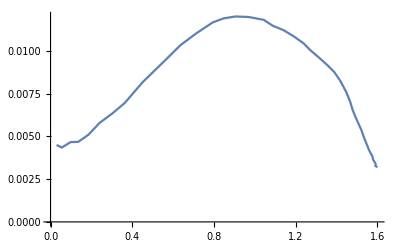

```mathematica
{b,b/h}//Transpose//ListLinePlot
```

```mathematica
ImageGraphics[RemoveBackground[-Graphics-],2]
```

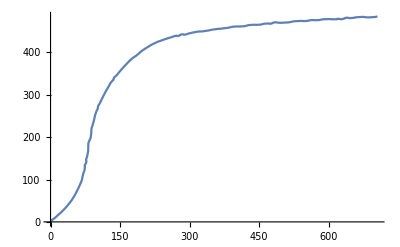

```mathematica
ImageGraphics[RemoveBackground[-Graphics-],2][[1,1,2;;-230]]//ListLinePlot
```

```mathematica
BMu=(Transpose[{B,B/H}]/.{_,Indeterminate}->Nothing);
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

```mathematica
order=6;
fitData=FindFit[BMu,Sum[Subscript[a, i]*x^i,{i,0,order}],Table[Subscript[a, i],{i,0,order}],x]
```

{a_0→0.0000379551,a_1→0.0000657508,a_2→-0.0000192507,a_3→0.000276913,a_4→-0.000409223,a_5→0.000209611,a_6→-0.0000380938}

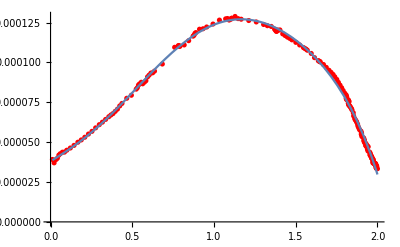

```mathematica
Show[ListPlot[BMu,PlotStyle->Red],Plot[∑_(i=0)^order Subscript[a, i] x^i/.fitData,{x,0.01131202650372895,2.}]]
```

```mathematica
fitData={Subscript[a, 0]->0.000037955129560483474,Subscript[a, 1]->0.00006575078254916768,Subscript[a, 2]->-0.000019250684240476186,Subscript[a, 3]->0.0002769129642720887,Subscript[a, 4]->-0.00040922344805632805,Subscript[a, 5]->0.0002096110387525365,Subscript[a, 6]->-0.00003809378487585398}
mu=Function[x,Evaluate[∑_(i=0)^order Subscript[a, i] x^i/.fitData]]
```